```mathematica
tExp1={0,24,48,72,96,120};(*h*)
ExcellCHO
XR11ExcellCHOExp1={0.3,0.286,0.755,0.78,1.57,1.776} ; (* ,1.85 cell/mL*)
XR12ExcellCHOExp1={0.3,0.306,0.625,0.766,1.6,2.14}   ; (* ,1.856*)

XR21ExcellCHOExp1={0.3,0.253,0.555,0.754,1.48,1.896} ; (*,1.85 cell/mL*) 
XR22ExcellCHOExp1={0.3,0.273,0.465,0.794,1.4,1.896}   ; (*,1.744*)

XR31ExcellCHOExp1={0.3,0.255,0.452,0.754,1.468,2.50} ; (*,1.84cell/mL*)
XR32ExcellCHOExp1={0.3,0.316,0.564,0.76,1.58,2.48}   ; (*,1.88*)


DMEMlow
XR11DMEMlowExp1={0.3,0.107,0.056,0,0,0} ; (*cell/mL*)
XR12DMEMlowExp1={0.3,0.12,0.08,0,0,0}   ;

XR21DMEMlowExp1={0.3,0.153,0.056,0,0,0} ; (*cell/mL*)
XR22DMEMlowExp1={0.3,0.135,0.03,0,0,0}   ;

XR31DMEMlowExp1={0.3,0.115,0.056,0,0,0} ; (*cell/mL*)
XR32DMEMlowExp1={0.3,0.108,0.08,0,0,0}   ;

tExp1DMEMF12={0,24,48,72,96,120};(*h*)
DMEMF12
XR11DMEMF12Exp1={0.3,0.51,0.864,1.44,1.365,1.73} ; (*cell/mL*)
XR12DMEMF12Exp1={0.3,0.487,0.825,1.64,1.35,1.68}   ;

XR21DMEMF12Exp1={0.3,0.45,0.73,1.214,1.27,1.328} ; (*cell/mL*)
XR22DMEMF12Exp1={0.3,0.5,0.74,1.426,1.29,1.576}   ;

XR31DMEMF12Exp1={0.3,0.536,0.905,1.62,1.2,1.44} ; (*cell/mL*)
XR32DMEMF12Exp1={0.3,0.47,1.03,1.686,1.27,1.496}   ;

Premium
XR11PremiumExp1={0.3,0.012,0.008,0,0,0} ; (*cell/mL*)
XR12PremiumExp1={0.3,0.016,0.004,0,0,0}   ;

XR21PremiumExp1={0.3,0.032,0.008,0,0,0} ; (*cell/mL*)
XR22PremiumExp1={0.3,0.02,0,0,0,0}   ;

XR31PremiumExp1={0.3,0.012,0,0,0,0} ; (*cell/mL*)
XR32PremiumExp1={0.3,0.024,0.008,0,0,0}   ;
```

ExcellCHO

DMEMlow

DMEMF12

Premium

```mathematica
XExcellCHOExp1Orden =Table[Sort[{XR11ExcellCHOExp1[[i]],XR12ExcellCHOExp1[[i]],XR21ExcellCHOExp1[[i]],XR22ExcellCHOExp1[[i]],XR31ExcellCHOExp1[[i]],XR32ExcellCHOExp1[[i]]},Less],{i,1,6}];
XDMEMF12Exp1Orden =Table[Sort[{XR11DMEMF12Exp1[[i]],XR12DMEMF12Exp1[[i]],XR21DMEMF12Exp1[[i]],XR22DMEMF12Exp1[[i]],XR31DMEMF12Exp1[[i]],XR32DMEMF12Exp1[[i]]},Less],{i,1,6}];
```

```mathematica
tExp1={0,24,48,72,96,120};

Table[tExp1[[i]],{i,1,Length[tExp1]},{j,1,6}]
```

{{0,0,0,0,0,0},{24,24,24,24,24,24},{48,48,48,48,48,48},{72,72,72,72,72,72},{96,96,96,96,96,96},{120,120,120,120,120,120}}

```mathematica
XExcellCHOExp1media = Table[Mean[{XR11ExcellCHOExp1[[i]],XR12ExcellCHOExp1[[i]],XR21ExcellCHOExp1[[i]],XR22ExcellCHOExp1[[i]],XR31ExcellCHOExp1[[i]],XR32ExcellCHOExp1[[i]]}],{i,6}];
XDMEMF12Exp1media = Table[Mean[{XR11DMEMF12Exp1[[i]],XR12DMEMF12Exp1[[i]],XR21DMEMF12Exp1[[i]],XR22DMEMF12Exp1[[i]],XR31DMEMF12Exp1[[i]],XR32DMEMF12Exp1[[i]]}],{i,6}];
```

```mathematica
XExcellCHOExp1Inter = Interpolation[{tExp1,{0.3,0.3,0.5693333333333334,0.7679999999999999,1.5163333333333335,2.114666666666667}}ᵀ];
XDMEMF12Exp1Inter = Interpolation[{tExp1,XDMEMF12Exp1media}ᵀ];
```

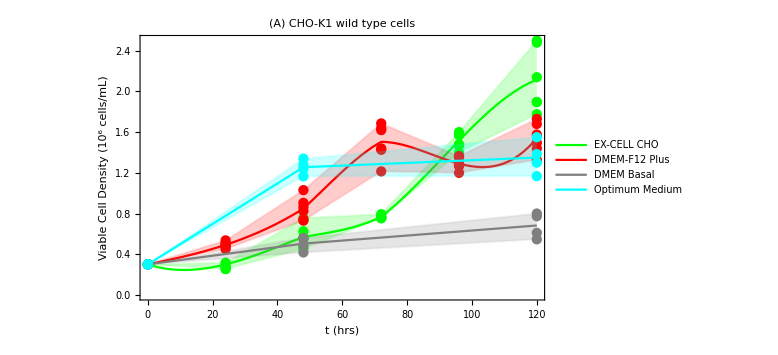

```mathematica
Show[{ListPlot[Table[{Table[Table[tExp1[[i]],{i,6}],{j,6}][[k]],Table[XExcellCHOExp1Orden [[j,i]],{i,6},{j,6}][[k]]}ᵀ,{k,{1,6}}],FrameLabel->{"t (hrs)","Viable Cell Density (10^6 cells/mL)"},Joined->True,Filling->{1->{2}},PlotStyle->Directive[Green,Opacity[0.1]],PlotLabel->Style["(A)           CHO-K1 wild type cells          ",20,Bold,Black],ImageSize->Large,LabelStyle->Directive[FontSize->16,Black],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Directive[Black,20,FontFamily->"LiberationSerif"]],ListPlot[Table[{Table[Table[tExp1[[i]],{i,6}],{j,6}][[k]],Table[XExcellCHOExp1Orden [[j,i]],{i,6},{j,6}][[k]]}ᵀ,{k,6}],FrameLabel->{"t (hrs)","Viable Cell Density (10^6 cells/mL)"},Joined->False,PlotStyle->Green],Plot[XExcellCHOExp1Inter[x],{x,0,120},PlotStyle->Green,PlotLegends->Placed[{"EX-CELL CHO"},{0.152,0.82}],LabelStyle->Directive[FontSize->16,Black]],
ListPlot[Table[{Table[Table[tExp1[[i]],{i,6}],{j,6}][[k]],Table[XDMEMF12Exp1Orden [[j,i]],{i,6},{j,6}][[k]]}ᵀ,{k,{1,6}}],Joined->True,Filling->{1->{2}},PlotStyle->Directive[Red,Opacity[0.1]],ImageSize->Large,LabelStyle->Directive[FontSize->16,Black],Axes->False,FrameStyle->Directive[Black,16,FontFamily->"LiberationSerif"]],ListPlot[Table[{Table[Table[tExp1[[i]],{i,6}],{j,6}][[k]],Table[XDMEMF12Exp1Orden [[j,i]],{i,6},{j,6}][[k]]}ᵀ,{k,6}],Joined->False,PlotStyle->Red],Plot[XDMEMF12Exp1Inter[x],{x,0,120},PlotStyle->Red,PlotLegends->Placed[{"DMEM-F12 Plus"},{0.165,0.75}],LabelStyle->Directive[FontSize->16,Black]]
,ListPlot[{XR12lowITSExp4NEW,XR22lowITSExp4NEW},Joined->True,Filling->{1->{2}},PlotStyle->Directive[Gray,Opacity[0.1]],ImageSize->Large,LabelStyle->Directive[FontSize->16,Black],Axes->False,FrameStyle->Directive[Black,16,FontFamily->"LiberationSerif"]],ListPlot[{XR11lowITSExp4NEW,XR12lowITSExp4NEW,XR21lowITSExp4NEW,XR22lowITSExp4NEW},PlotStyle->Gray],ListPlot[Xlowmedia,PlotStyle->Gray,Joined->True,PlotLegends->Placed[{"DMEM Basal"},{0.14,0.68}],LabelStyle->Directive[FontSize->16,Black]],ListPlot[{XR11PremiumITSExp2,XR21PremiumITSExp2},Joined->True,Filling->{1->{2}},PlotStyle->Directive[Cyan,Opacity[0.1]],ImageSize->Large,LabelStyle->Directive[FontSize->16,Black],Axes->False,FrameStyle->Directive[Black,16,FontFamily->"LiberationSerif"]],ListPlot[{XR11PremiumITSExp2,XR12PremiumITSExp2,XR21PremiumITSExp2,XR22PremiumITSExp2},PlotStyle->Cyan],ListPlot[XPremiumExp1media,PlotStyle->Cyan,Joined->True,PlotLegends->Placed[{"Optimum Medium"},{0.174,0.6}],LabelStyle->Directive[FontSize->16,Black]]}]
```

```mathematica
XPremiumExp1media = Table[Mean[{XR11PremiumITSExp2[[i]],XR12PremiumITSExp2[[i]],XR21PremiumITSExp2[[i]],XR22PremiumITSExp2[[i]]}],{i,3}];
Xlowmedia =  Table[Mean[{XR11lowITSExp4NEW[[i]],XR12lowITSExp4NEW[[i]],XR21lowITSExp4NEW[[i]],XR22lowITSExp4NEW[[i]]}],{i,3}]
```

{{0,0.3},{48,0.50425},{120,0.68225}}

```mathematica
XPremiumExp1Inter = Interpolation[XPremiumExp1media];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

```mathematica
XR11PremiumITSExp1={{0,0.15},{72,0.972}};
XR12PremiumITSExp1={{0,0.15},{72,1.04}};
XR21PremiumITSExp1={{0,0.15},{72,0.992}};
XR22PremiumITSExp1={{0,0.15},{72,1.0}};

XR11PremiumITSExp3={{0,0.15},{72,0.787}}; (*19/06*)
XR12PremiumITSExp3={{0,0.15},{72,0.68}};
XR21PremiumITSExp3={{0,0.15},{72,0.78}};
XR22PremiumITSExp3={{0,0.15},{72,0.987}};

XR11PremiumITSExp2={{0,0.3},{48,1.165},{120,1.167}};(*17/06*)
XR12PremiumITSExp2={{0,0.3},{48,1.275},{120,1.384}};
XR21PremiumITSExp2={{0,0.3},{48,1.34},{120,1.55}};
XR22PremiumITSExp2={{0,0.3},{48,1.24},{120,1.3}};

XR11PremiumITSExp4={{0,0.3},{48,0.817}};(*22/06*)
XR12PremiumITSExp4={{0,0.3},{48,0.98}};
XR21PremiumITSExp4={{0,0.3},{48,0.8}};
XR22PremiumITSExp4={{0,0.3},{48,0.77}};


XR11lowITSExp4NEW={{0,0.3},{48,0.49},{120,0.61}};(*22/06*)
XR12lowITSExp4NEW={{0,0.3},{48,0.417},{120,0.546}};
XR21lowITSExp4NEW={{0,0.3},{48,0.55},{120,0.773}};
XR22lowITSExp4NEW={{0,0.3},{48,0.56},{120,0.8}};

XR11lowITSExp1={{0,0.15},{72,0.61}};
XR12lowITSExp1={{0,0.15},{72,0.65}};
XR21lowITSExp1={{0,0.15},{72,0.784}};
XR22lowITSExp1={{0,0.15},{72,0.728}};

XR11lowITSExp2={{0,0.3},{48,1.056},{120,0.8}};(*17/06*)
XR12lowITSExp2={{0,0.3},{48,1.032},{120,0.773}};
XR21lowITSExp2={{0,0.3},{48,1.24},{120,0.61}};
XR22lowITSExp2={{0,0.3},{48,0.873},{120,0.546}};

XR11lowITSExp3={{0,0.15},{72,0.827}};(*19/06*)
XR12lowITSExp3={{0,0.15},{72,0.847}};
XR21lowITSExp3={{0,0.15},{72,0.515}};
XR22lowITSExp3={{0,0.15},{72,0.71}};

XR11lowITSExp4={{0,0.3},{48,0.49}};(*22/06*)
XR12lowITSExp4={{0,0.3},{48,0.417}};
XR21lowITSExp4={{0,0.3},{48,0.55}};
XR22lowITSExp4={{0,0.3},{48,0.56}};
```

## Cultivo CHO_RBD (22/06)

```mathematica
tExp1RBD={0,24,48,120};(*h*)
ExcellCHO
RBDXR11ExcellCHOExp1={0.3,0.50667,1.41,1.7} ; (*cell/mL*)
RBDXR12ExcellCHOExp1={0.3,0.54,1.532,1.72}   ;

RBDXR21ExcellCHOExp1={0.3,0.54,1.293,1.76} ; (*cell/mL*)
RBDXR22ExcellCHOExp1={0.3,0.427,1.293,1.86}   ;

RBDXR31ExcellCHOExp1={0.3,0.46,1.23,1.8} ; (*cell/mL*)
RBDXR32ExcellCHOExp1={0.3,0.567,1.512,1.892}   ;

DMEMF12
RBDXR11DMEMF12Exp1={0.3,0.385,0.424,0.2} ; (*cell/mL*)
RBDXR12DMEMF12Exp1={0.3,0.466,0.432,0.4}  ;

RBDXR21DMEMF12Exp1={0.3,0.33,0.455,0.452} ; (*cell/mL*)
RBDXR22DMEMF12Exp1={0.3,0.212,0.42,0.452} ;

RBDXR31DMEMF12Exp1={0.3,0.394,0.508,0.4} ; (*cell/mL*)
RBDXR32DMEMF12Exp1={0.3,0.36,0.495,0.468} ;
```

ExcellCHO

DMEMF12

```mathematica
RBDExcellCHOmedia=Table[Mean[{RBDXR11ExcellCHOExp1[[i]],RBDXR12ExcellCHOExp1[[i]],RBDXR21ExcellCHOExp1[[i]],RBDXR22ExcellCHOExp1[[i]],RBDXR31ExcellCHOExp1[[i]],RBDXR32ExcellCHOExp1[[i]]}],{i,1,4}];
RBDDMEMF12media=Table[Mean[{RBDXR11DMEMF12Exp1[[i]],RBDXR12DMEMF12Exp1[[i]],RBDXR21DMEMF12Exp1[[i]],RBDXR22DMEMF12Exp1[[i]],RBDXR31DMEMF12Exp1[[i]],RBDXR32DMEMF12Exp1[[i]]}],{i,1,4}];
RBDXDMEMF12Exp1Inter = Interpolation[{tExp1RBD,RBDDMEMF12media}ᵀ];
RBDXExcellCHOExp1Inter = Interpolation[{tExp1RBD,RBDExcellCHOmedia}ᵀ];
RBDXExcellCHOExp1Orden =Table[Sort[{RBDXR11ExcellCHOExp1[[i]],RBDXR12ExcellCHOExp1[[i]],RBDXR21ExcellCHOExp1[[i]],RBDXR22ExcellCHOExp1[[i]],RBDXR31ExcellCHOExp1[[i]],RBDXR32ExcellCHOExp1[[i]]},Less],{i,1,4}];
RBDXDMEMF12Exp1Orden =Table[Sort[{RBDXR11DMEMF12Exp1[[i]],RBDXR12DMEMF12Exp1[[i]],RBDXR21DMEMF12Exp1[[i]],RBDXR22DMEMF12Exp1[[i]],RBDXR31DMEMF12Exp1[[i]],RBDXR32DMEMF12Exp1[[i]]},Less],{i,1,4}];
```

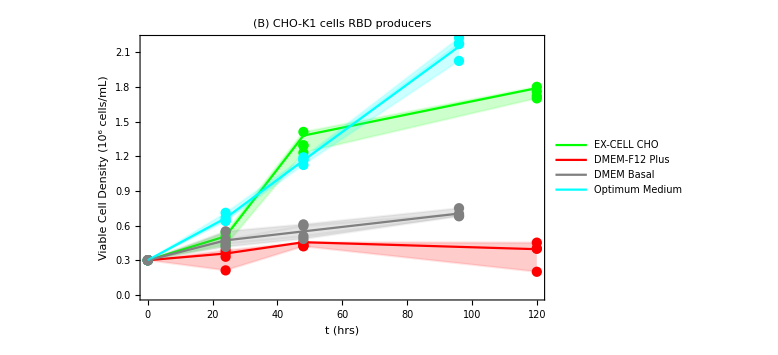

```mathematica
Show[{ListPlot[Table[{Table[Table[tExp1RBD[[i]],{i,4}],{j,4}][[k]],Table[RBDXExcellCHOExp1Orden [[j,i]],{i,4},{j,4}][[k]]}ᵀ,{k,{1,4}}],FrameLabel->{"t (hrs)","Viable Cell Density (10^6 cells/mL)"},Joined->True,Filling->{1->{2}},PlotStyle->Directive[Green,Opacity[0.1]],PlotLabel->Style["(B)           CHO-K1 cells RBD producers          ",20, Bold,Black],ImageSize->Large,LabelStyle->Directive[FontSize->16,Black],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Directive[Black,20,FontFamily->"LiberationSerif"],PlotRange->{0,2.2}],ListPlot[Table[{Table[Table[tExp1RBD[[i]],{i,4}],{j,4}][[k]],Table[RBDXExcellCHOExp1Orden [[j,i]],{i,4},{j,4}][[k]]}ᵀ,{k,4}],Joined->False,PlotStyle->Green],
ListPlot[Table[{Table[Table[tExp1RBD[[i]],{i,4}],{j,4}][[k]],Table[RBDXDMEMF12Exp1Orden [[j,i]],{i,4},{j,4}][[k]]}ᵀ,{k,{1,4}}],Joined->True,Filling->{1->{2}},PlotStyle->Directive[Red,Opacity[0.1]],ImageSize->Large,LabelStyle->Directive[FontSize->16,Black],Axes->False,FrameStyle->Directive[Black,16,FontFamily->"LiberationSerif"]],ListPlot[Table[{Table[Table[tExp1RBD[[i]],{i,4}],{j,4}][[k]],Table[RBDXDMEMF12Exp1Orden [[j,i]],{i,4},{j,4}][[k]]}ᵀ,{k,4}],Joined->False,PlotStyle->Red],
ListPlot[{tExp1RBD,RBDExcellCHOmedia}ᵀ,PlotStyle->Green,PlotLegends->Placed[{"EX-CELL CHO"},{0.154,0.9}],Joined->True,LabelStyle->Directive[FontSize->16,Black]],ListPlot[{tExp1RBD,RBDDMEMF12media}ᵀ,PlotStyle->Red,PlotLegends->Placed[{"DMEM-F12 Plus"},{0.163,0.82}],Joined->True,LabelStyle->Directive[FontSize->16,Black]],ListPlot[{RBDXR11PremiumITSExp2,RBDXR12PremiumITSExp2,RBDXR21PremiumITSExp2,RBDXR22PremiumITSExp2},PlotStyle->Cyan,PlotRange->All],ListPlot[{RBDXR11lowITSExp2,RBDXR12lowITSExp2,RBDXR21lowITSExp2,RBDXR22lowITSExp2},PlotStyle->Gray,PlotRange->All],ListPlot[RBDlowITSmedia,Joined->True,PlotStyle->Gray,PlotLegends->Placed[{"DMEM Basal"},{0.135,0.75}],LabelStyle->Directive[FontSize->16,Black]],ListPlot[RBDPremiumITSmedia,Joined->True,PlotStyle->Cyan,PlotLegends->Placed[{"Optimum Medium"},{0.17,0.685}],LabelStyle->Directive[FontSize->16,Black]],ListPlot[Table[{Table[Table[tITS[[i]],{i,4}],{j,4}][[k]],Table[RBDXPremiumITSOrden [[j,i]],{i,4},{j,4}][[k]]}ᵀ,{k,4}] ,Joined->True,Filling->{1->{4}},PlotStyle->Directive[Cyan,Opacity[0.1]]],ListPlot[Table[{Table[Table[tITS[[i]],{i,4}],{j,4}][[k]],Table[RBDXlowITSOrden [[j,i]],{i,4},{j,4}][[k]]}ᵀ,{k,4}] ,Joined->True,Filling->{1->{4}},PlotStyle->Directive[Gray,Opacity[0.1]]]}]
```

```mathematica
RBDXR11PremiumITSExp2={{0,0.3},{24,0.64},{48,1.124},{96,2.224}};
RBDXR12PremiumITSExp2={{0,0.3},{24,0.667},{48,1.165},{96,2.176}};
RBDXR21PremiumITSExp2={{0,0.3},{24,0.64},{48,1.172},{96,2.17}};
RBDXR22PremiumITSExp2={{0,0.3},{24,0.71},{48,1.19},{96,2.024}};

RBDXR11lowITSExp2={{0,0.3},{24,0.476},{48,0.508},{96,0.68}};
RBDXR12lowITSExp2={{0,0.3},{24,0.445},{48,0.484},{96,0.685}};
RBDXR21lowITSExp2={{0,0.3},{24,0.415},{48,0.596},{96,0.7}};
RBDXR22lowITSExp2={{0,0.3},{24,0.55},{48,0.61},{96,0.75}};
```

```mathematica
tITS={0,24,48,96};
```

```mathematica
RBDPremiumITSmedia=Table[Mean[{RBDXR11PremiumITSExp2[[i]],RBDXR12PremiumITSExp2[[i]],RBDXR21PremiumITSExp2[[i]],RBDXR22PremiumITSExp2[[i]]}],{i,4}];
RBDlowITSmedia=Table[Mean[{RBDXR11lowITSExp2[[i]],RBDXR12lowITSExp2[[i]],RBDXR21lowITSExp2[[i]],RBDXR22lowITSExp2[[i]]}],{i,4}];
```

```mathematica
RBDXPremiumITSOrden =Table[Sort[{RBDXR11PremiumITSExp2[[i]][[2]],RBDXR12PremiumITSExp2[[i]][[2]],RBDXR21PremiumITSExp2[[i]][[2]],RBDXR22PremiumITSExp2[[i]][[2]]},Less],{i,1,4}]
RBDXlowITSOrden =Table[Sort[{RBDXR11lowITSExp2[[i]][[2]],RBDXR12lowITSExp2[[i]][[2]],RBDXR21lowITSExp2[[i]][[2]],RBDXR22lowITSExp2[[i]][[2]]},Less],{i,1,4}]
```

{{0.3,0.3,0.3,0.3},{0.64,0.64,0.667,0.71},{1.124,1.165,1.172,1.19},{2.024,2.17,2.176,2.224}}

{{0.3,0.3,0.3,0.3},{0.415,0.445,0.476,0.55},{0.484,0.508,0.596,0.61},{0.68,0.685,0.7,0.75}}